# Resultados prácticas

Amado Cabrera

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

## Definiendo variables

```mathematica
clrs=RGBColor[#]&/@({"#d8d97a","#95c36e","#74c8c3","#5a97c1","#295384","#0a2e57"}[[{4,2,5,3,1,6}]]);
```

```mathematica
qlabels=MaTeX[#,
Magnification->1.4,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\text{Posición }\\ket{x}","\\text{Probabilidad }\\mel{x}{\\rho_X}{x}"};
clabels=MaTeX[#,
Magnification->1.4,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\text{Posición }x","\\text{Probabilidad }P(x)"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

## Inicializaciones

```mathematica
dimensions={2,201};
InitializeDTQW@@dimensions;
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

## Resultados

### Estados usuales

Primero replicaremos los resultados más populares de caminatas cuánticas

```mathematica
psi00=VectorState[{{1,0,0}}];
```

```mathematica
rho00=#.#†&@DTQW2[psi00,100];
```

```mathematica
prob00=Diagonal@MatrixPartialTrace[rho00,1,dimensions];
```

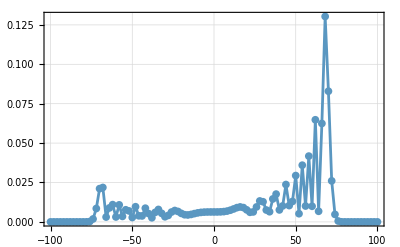

```mathematica
plt00=ListLinePlot[Transpose[{Range[-100,100],prob00}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"plt00.pdf",plt00];
```

```mathematica
psi10=VectorState[{{1,1,0}}];
```

```mathematica
rho10=#.#†&@DTQW2[psi10,100];
```

```mathematica
prob10=Diagonal@MatrixPartialTrace[rho10,1,dimensions];
```

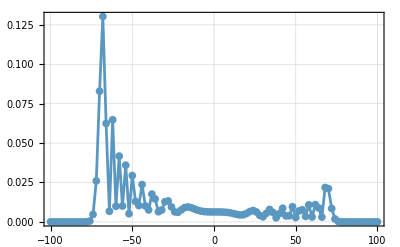

```mathematica
plt10=ListLinePlot[Transpose[{Range[-100,100],prob10}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"plt10.pdf",plt10];
```

### Superposiciones en la moneda

Geometricamente equidistantes

#### Estados +,0 y -,0

```mathematica
psip0=VectorState[{{1/Sqrt[2],0,0},{1/Sqrt[2],1,0}}];
```

```mathematica
rhop0=#.#†&@DTQW2[psip0,100];
```

```mathematica
probp0=Diagonal@MatrixPartialTrace[rhop0,1,dimensions];
```

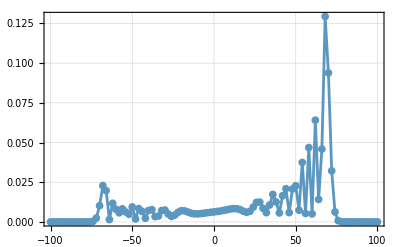

```mathematica
pltp0=ListLinePlot[Transpose[{Range[-100,100],probp0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltp0.pdf",pltp0];
```

```mathematica
psim0=VectorState[{{1/Sqrt[2],0,0},{-1/Sqrt[2],1,0}}];
```

```mathematica
rhom0=#.#†&@DTQW2[psim0,100];
```

```mathematica
probm0=Diagonal@MatrixPartialTrace[rhom0,1,dimensions];
```

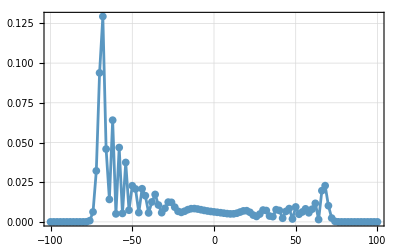

```mathematica
pltm0=ListLinePlot[Transpose[{Range[-100,100],probm0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltm0.pdf",pltm0];
```

#### Estados +_y,0 y -_y,0

```mathematica
psipy0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhopy0=#.#†&@DTQW2[psipy0,100];
```

```mathematica
probpy0=Diagonal@MatrixPartialTrace[rhopy0,1,dimensions];
```

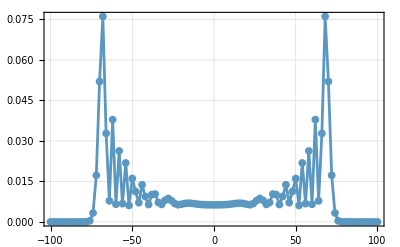

```mathematica
pltpy0=ListLinePlot[Transpose[{Range[-100,100],probpy0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltpy0.pdf",pltpy0];
```

```mathematica
psimy0=VectorState[{{1/Sqrt[2],0,0},{-ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhomy0=#.#†&@DTQW2[psimy0,100];
```

```mathematica
probmy0=Diagonal@MatrixPartialTrace[rhomy0,1,dimensions];
```

```mathematica
pltmy0=ListLinePlot[Transpose[{Range[-100,100],probmy0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pltmy0.pdf",pltmy0];
```

### Estados superpuestos en la posición

```mathematica
psi0sp=VectorState[{{1/Sqrt[2],0,-20},{1/Sqrt[2],0,20}}];
```

```mathematica
rho0sp=#.#†&@DTQW2[psi0sp,100];
```

```mathematica
prob0sp=Diagonal@MatrixPartialTrace[rho0sp,1,dimensions];
```

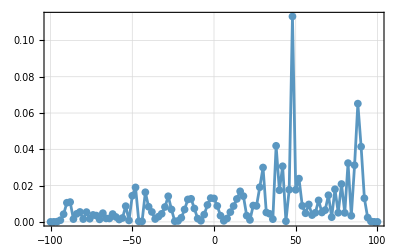

```mathematica
plt0sp=ListLinePlot[Transpose[{Range[-100,100],prob0sp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"plt0sp.pdf",plt0sp];
```

```mathematica
psi0sm=VectorState[{{1/Sqrt[2],0,-20},{-1/Sqrt[2],0,20}}];
```

```mathematica
rho0sm=#.#†&@DTQW2[psi0sm,100];
```

```mathematica
prob0sm=Diagonal@MatrixPartialTrace[rho0sm,1,dimensions];
```

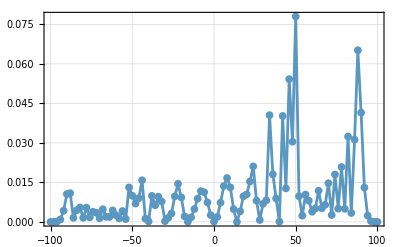

```mathematica
plt0sm=ListLinePlot[Transpose[{Range[-100,100],prob0sm}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"plt0sm.pdf",plt0sm];
```

```mathematica
psi1sp=VectorState[{{1/Sqrt[2],1,-20},{1/Sqrt[2],1,20}}];
```

```mathematica
rho1sp=#.#†&@DTQW2[psi1sp,100];
```

```mathematica
prob1sp=Diagonal@MatrixPartialTrace[rho1sp,1,dimensions];
```

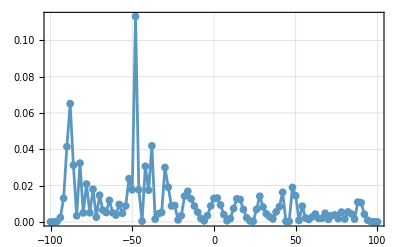

```mathematica
plt1sp=ListLinePlot[Transpose[{Range[-100,100],prob1sp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"plt1sp.pdf",plt1sp];
```

### Superposición en ambos espacios

```mathematica
psipsp=VectorState[{{1/2,0,-20},{1/2,1,-20},{1/2,0,20},{1/2,1,20}}];
```

```mathematica
rhopsp=#.#†&@DTQW2[psipsp,100];
```

```mathematica
probpsp=Diagonal@MatrixPartialTrace[rhopsp,1,dimensions];
```

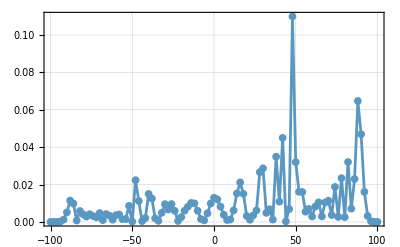

```mathematica
pltpsp=ListLinePlot[Transpose[{Range[-100,100],probpsp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltpsp.pdf",pltpsp];
```

```mathematica
psimsp=VectorState[{{1/2,0,-20},{-1/2,1,-20},{1/2,0,20},{-1/2,1,20}}];
```

```mathematica
rhomsp=#.#†&@DTQW2[psimsp,100];
```

```mathematica
probmsp=Diagonal@MatrixPartialTrace[rhomsp,1,dimensions];
```

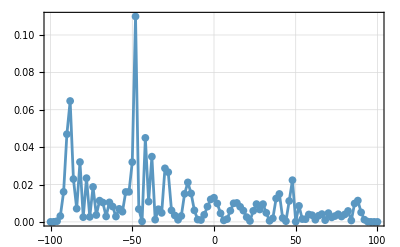

```mathematica
pltmsp=ListLinePlot[Transpose[{Range[-100,100],probmsp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltmsp.pdf",pltmsp];
```

```mathematica
psipysp=VectorState[{{1/2,0,-20},{ⅈ/2,1,-20},{1/2,0,20},{ⅈ/2,1,20}}];
```

```mathematica
rhopysp=#.#†&@DTQW2[psipysp,100];
```

```mathematica
probpysp=Diagonal@MatrixPartialTrace[rhopysp,1,dimensions];
```

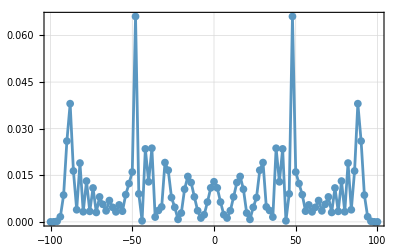

```mathematica
pltpysp=ListLinePlot[Transpose[{Range[-100,100],probpysp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltpysp.pdf",pltpysp];
```

### Estados entrelazados

```mathematica
psiptp=VectorState[{{1/Sqrt[2],0,-20},{1/Sqrt[2],1,20}}];
```

```mathematica
rhoptp=#.#†&@DTQW2[psiptp,100];
```

```mathematica
probptp=Diagonal@MatrixPartialTrace[rhoptp,1,dimensions];
```

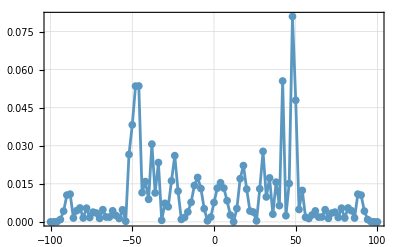

```mathematica
pltptp=ListLinePlot[Transpose[{Range[-100,100],probptp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltptp.pdf",pltptp];
```

```mathematica
psipytp=VectorState[{{1/Sqrt[2],0,-20},{ⅈ/Sqrt[2],1,20}}];
```

```mathematica
rhopytp=#.#†&@DTQW2[psipytp,100];
```

```mathematica
probpytp=Diagonal@MatrixPartialTrace[rhopytp,1,dimensions];
```

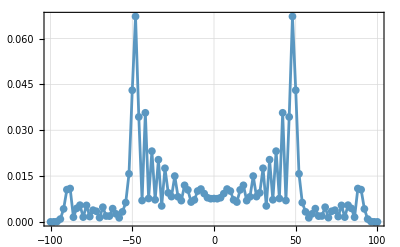

```mathematica
pltpytp=ListLinePlot[Transpose[{Range[-100,100],probpytp}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->qlabels
]
```

### Caminata aleatoria clásica

```mathematica
Export[NotebookDirectory[]<>"pltpytp.pdf",pltpytp];
```

```mathematica
probclassic=Riffle[Binomial[#,Range[0,#]]/2^#,0]&@100//N;
```

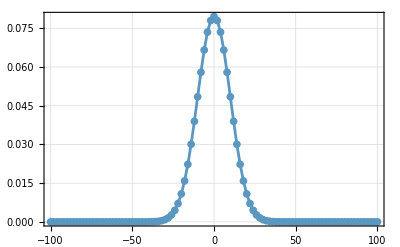

```mathematica
pltclassic=ListLinePlot[Transpose[{Range[-100,100],probclassic}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs[[1]],
FrameLabel->clabels
]
```

```mathematica
Export[NotebookDirectory[]<>"pltclassic.pdf",pltclassic];
```

### Dinámica de qubit en campo magnético

```mathematica
vec=Module[
{a,b,c,d},
Hamiltonian=Subscript[μ, B] Subscript[B, z] PauliMatrix[3];
Unitary=MatrixExp[-ⅈ t Hamiltonian/hbar];
ρ=(PauliMatrix[0]+{Sin[θ]Sin[ϕ],Sin[θ]Cos[ϕ],Cos[θ]}.PauliMatrix[Range[3]])/2/.{θ->π/3,ϕ->π/4};
ρ2=Unitary.ρ.Unitary†;
{{a,b},{c,d}}=ρ2;
FullSimplify[{2Re[c],2Im[c],2a-1}/.{hbar->1,Subscript[μ, B]->1,Subscript[B, z]->1},Assumptions->t∈Reals]
]
```

{√6 Re[(1/4+ⅈ/4) ⅇ^(2 ⅈ t)],√6 Im[(1/4+ⅈ/4) ⅇ^(2 ⅈ t)],1/2}

```mathematica
sphere=Show[
ParametricPlot3D[{Sin[θ]Sin[ϕ],Sin[θ]Cos[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},
PlotStyle->Directive[Opacity[0.1],Gray],
MeshStyle->Gray,
Boxed->False,
Axes->False,
PlotRange->({#,#,#}&@(1.1{-1.25,1.25})),

],
ParametricPlot3D[vec,{t,0,π},
PlotStyle->Directive[Thick,Orange]
],
Graphics3D[{
Line[vals=Map[RotateLeft@@#&,({{{-1.25,0,0},#},{{1.25,0,0},#}}&/@Range[3]),{2}]],
Evaluate@MapThread[Text,{
{"1","0","-_y","+_y","-","+"},
1.05Flatten[vals,1]
}]
}]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"sphere.pdf",sphere]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/sphere.pdf